# Stochastic Gompertz model for yeast lifespan

## Data sets information

The RLS data used here are from Kaeberlein et al 2004, Plos Genetics http://journals.plos.org/plosbiology/article?id=10.1371/journal.pbio.0020296

The original data set is at https://doi.org/10.1371/journal.pbio.0020296.sd002

## Import data

Data sets name : data2-BY4742, d2-sir2, d3-by4742.SIR2.ox.2glucose, d4-fob1, d5-hxk2, d6-fob1.hxk2

```mathematica
NotebookDirectory[]
```

C:\Users\Ziwei Ma\OneDrive - University of Tennessee at Chattanooga\Research\2020\

```mathematica
SetDirectory[NotebookDirectory[]]
d1=Import["RLSdata\\kaeberlein04_selected_strains1.csv"];
d2=Import["RLSdata\\sir2.csv"];
d3=Import["RLSdata\\glocus2.csv"];
d4=Import["RLSdata\\fob1.csv"];
d5=Import["RLSdata\\hxk2.csv"];
d6=Import["RLSdata\\fob1hxk2.csv"];
```

C:\Users\Ziwei Ma\OneDrive - University of Tennessee at Chattanooga\Research\2020

## Empirical description

### Histograms of RLS

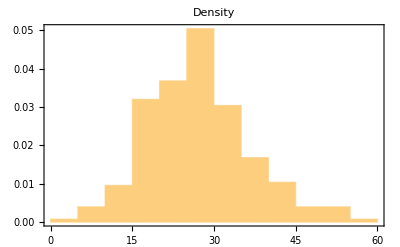
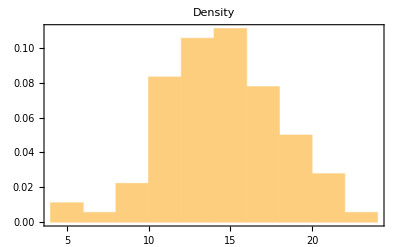
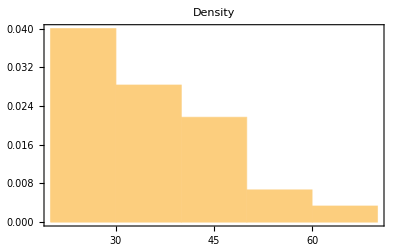
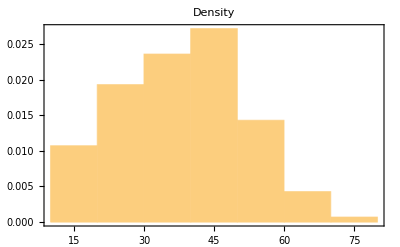
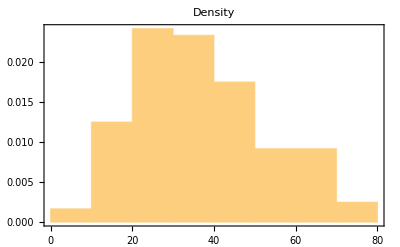
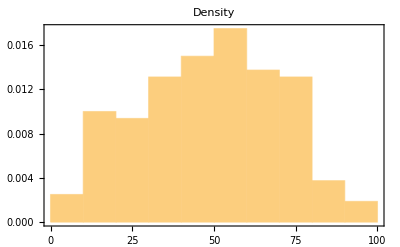

```mathematica
histo=Table[Histogram[a[[All,1]],Automatic,"PDF",Frame->True,PlotLabel->"Density"],{a,{d1,d2,d3,d4,d5,d6}}]
```

### Empirical survival curves

```mathematica
𝒟1=SurvivalDistribution[d1[[All,1]]];
𝒟2=SurvivalDistribution[d2[[All,1]]];𝒟3=SurvivalDistribution[d3[[All,1]]];𝒟4=SurvivalDistribution[d4[[All,1]]];𝒟5=SurvivalDistribution[d5[[All,1]]];𝒟6=SurvivalDistribution[d6[[All,1]]];
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

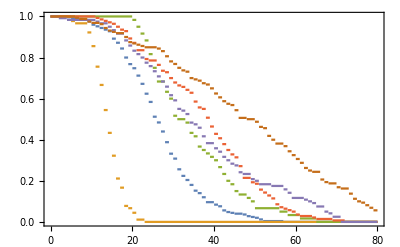

```mathematica
Needs["PlotLegends`"]
names = {"BY4742","sir2","by4742.SIR2.ox.2glucose","fob1","hxk2","fob1.hxk2"};
Plot[Evaluate@Table[SurvivalFunction[a,x],{a,{𝒟1,𝒟2,𝒟3,𝒟4,𝒟5,𝒟6}}],{x,0,80}, Frame->True, PlotLegend->names,LegendPosition->{1.1,-0.4}]
```

## Empirical models

```mathematica
𝒮1=SurvivalModelFit[d1[[All,1]]];
𝒮2=SurvivalModelFit[d2[[All,1]]];
𝒮3=SurvivalModelFit[d3[[All,1]]];
𝒮4=SurvivalModelFit[d4[[All,1]]];
𝒮5=SurvivalModelFit[d5[[All,1]]];
𝒮6=SurvivalModelFit[d6[[All,1]]];
```

### Empirical mortality rates

Power::infy: Infinite expression 1/0. encountered.

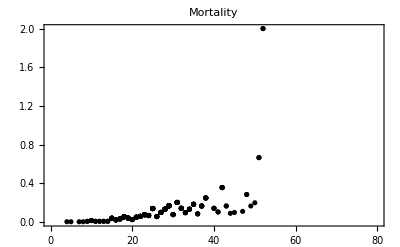

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

```mathematica
em1=ListPlot[Table[{a,𝒮1["HF"][a]},{a,data2[[All,1]]}],PlotStyle->{Black, Thick},Frame->True,PlotRange->{{0,80},All},PlotLabel->"Mortality"]
em2=ListPlot[Table[{a,𝒮2["HF"][a]},{a,d2[[All,1]]}],PlotStyle->{Blue, Thick},Frame->True,PlotRange->{{0,80},All},PlotLabel->"Mortality"];
em3=ListPlot[Table[{a,𝒮3["HF"][a]},{a,d3[[All,1]]}],PlotStyle->{Green, Thick},Frame->True,PlotRange->{{0,80},All},PlotLabel->"Mortality"];
em4=ListPlot[Table[{a,𝒮4["HF"][a]},{a,d3[[All,1]]}],PlotStyle->{Yellow, Thick},Frame->True,PlotRange->{{0,80},All},PlotLabel->"Mortality"];
em5=ListPlot[Table[{a,𝒮5["HF"][a]},{a,d5[[All,1]]}],PlotStyle->{Purple, Thick},Frame->True,PlotRange->{{0,80},All},PlotLabel->"Mortality"];
em6=ListPlot[Table[{a,𝒮6["HF"][a]},{a,d6[[All,1]]}],PlotStyle->{Black, Thick},Frame->True,PlotRange->{{0,80},All},PlotLabel->"Mortality"];
```

## Fitted Gompertz Model

We begin with a basic Gompertz model which has two parameters, scale parameter λ, and frailty parameter ξ, i.e. the mortality rate r(t)=ξ λ ⅇ^(λ t).

```mathematica
e𝒟1=EstimatedDistribution[d1[[All,1]],GompertzMakehamDistribution[λ,ξ]]
e𝒟2=EstimatedDistribution[d2[[All,1]],GompertzMakehamDistribution[λ,ξ]];
e𝒟3=EstimatedDistribution[d3[[All,1]],GompertzMakehamDistribution[λ,ξ]];
e𝒟4=EstimatedDistribution[d4[[All,1]],GompertzMakehamDistribution[λ,ξ]];
e𝒟5=EstimatedDistribution[d5[[All,1]],GompertzMakehamDistribution[λ,ξ]];
e𝒟6=EstimatedDistribution[d6[[All,1]],GompertzMakehamDistribution[λ,ξ]];
```

GompertzMakehamDistribution[0.0854466,0.0769792]

For example, the fitted density function, survival function and mortality rate are given below.

```mathematica
Table[f[e𝒟1,x],{f,{PDF,SurvivalFunction,HazardFunction}}]
```

{Piecewise[{{0.00657761 ⅇ^(0.0769792 (1-ⅇ^(0.0854466 x))+0.0854466 x), x≥0}, {0, True}}],Piecewise[{{ⅇ^(0.0769792 (1-ⅇ^(0.0854466 x))), x≥0}, {1, True}}],Piecewise[{{0.00657761 ⅇ^(0.0854466 x), x≥0}, {0, True}}]}

There are several plots below showing the empirical density (histogram), survival curve and mortality rate and their fitted Gompertz curves.

### Density

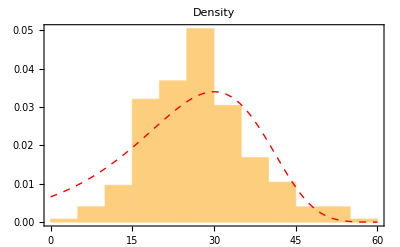

```mathematica
Show[{histo[[1]],Plot[PDF[e𝒟1,x],{x,0,60},PlotStyle->{Thick, Dashed, Red},PlotLabel->"Density",Frame->True,PlotRange->{0,0.06}]}]
```

### Survival

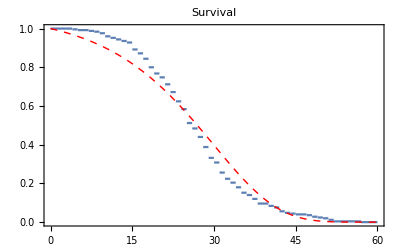

```mathematica
ems1=Plot[SurvivalFunction[𝒟1,x],{x,0,60},Frame->True,PlotLabel->"Survival"];
es1=Plot[SurvivalFunction[e𝒟1,x],{x,0,60},Frame->True,PlotStyle->{Thick, Dashed, Red}];
Show[ems1,es1]
```

### Mortality

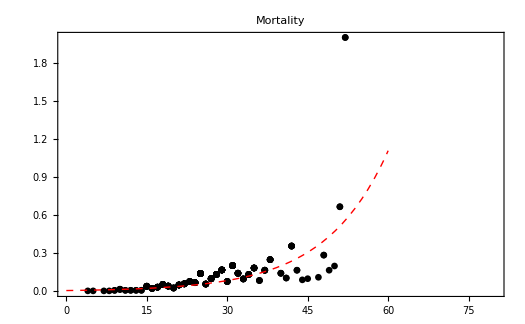

```mathematica
er1=Plot[HazardFunction[e𝒟1,x],{x,0,60},Frame->True,PlotStyle->{Thick, Dashed, Red}];
Show[em1,er1]
```

### Stochastic Differential Equation (SDE) Model

From above plots, especially the empirical mortality rates indicate some fluctuation around the fitted curve which describes the average mortality rate at each time t. By the definition of mortality rate

(d Log S(t))/dt=-r(t)

We can add a white noise into above differential equation

(d Log S(t))/dt=-r(t)+σ(t)ξ(t)

where ξ(t) is the white noise and σ(t) is a scale function of the white noise which describes the strength of the white noise. To complete the above SDE model, we need to estimate the scale function σ(t). Based on the empirical mortality rates, we calculate the standard deviation for lifespan groups, 10,20, 30,40 and 50, then find a simple function to fit.

```mathematica
sd1=Import["t1-sd.csv"];
```

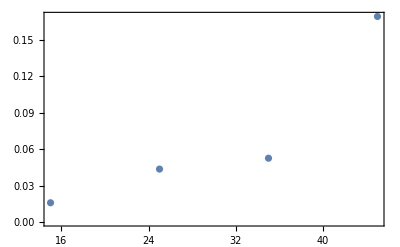

```mathematica
ListPlot[sd1,Frame->True]
```